## Process Points Function

```mathematica
(*dis=Table[First[NMinimize[(x-speedD[[i]])^2+(8.67Log[ x ]-30.75-freqD[[i]]/2)^2,{x,150,500}]],{i,1,Length[speedD]}]*)
closedranges[speedFreq_,speedstride_,freqEQ_,strideEQ_,npoints_]:=Module[{distances,first50closed,positioncloset,positioncloset2,speedrange,freqrange,distances2,first50closet2,speedrange2,freqrange2,positionF,speedfreqcloset,speedstridecloset,speedFC,speedSC,expfreq,expstride,thfreq,thstride,perdiffFreq,perdiffstride},

freqFunc[t]=freqEQ;
distances=Table[EuclideanDistance[speedFreq[[i]],{speedFreq[[i,1]],(freqFunc[t]/.t-> speedFreq[[i,1]] )}],{i,1,Length[speedFreq]}];
first50closed=Sort[distances][[;;npoints]];
positioncloset=Table[Position[distances,first50closed[[i]]],{i,1,Length[first50closed]}]//Flatten;
speedrange=Sort[Map[#[[1]]&,speedFreq[[positioncloset]]]];
freqrange=Sort[Map[#[[2]]&,speedFreq[[positioncloset]]]];


strideFunc[t]=strideEQ;
distances2=Table[EuclideanDistance[speedstride[[i]],{speedstride[[i,1]],(strideFunc[t]/.t->speedstride[[i,1]] )}],{i,1,Length[speedstride]}];
first50closet2=Sort[distances2][[;;npoints]];
positioncloset2=Table[Position[distances2,first50closet2[[i]]],{i,1,Length[first50closet2]}]//Flatten;
speedrange2=Sort[Map[#[[1]]&,speedstride[[positioncloset2]]]];
freqrange2=Sort[Map[#[[2]]&,speedstride[[positioncloset2]]]];

positionF=DeleteDuplicates[Join[positioncloset,positioncloset2]];

speedfreqcloset=speedFreq[[positioncloset]];
speedstridecloset=speedstride[[positioncloset2]];
speedFC=Map[First,speedfreqcloset];
speedSC=Map[First,speedstridecloset];
expfreq=freqFunc[t]/.t->speedFC;
expstride=strideFunc[t]/.t->speedSC;
thfreq=Map[Last,speedfreqcloset];
thstride=Map[Last,speedstridecloset];
perdiffFreq=Abs[((expfreq-thfreq)/expfreq)*100];
perdiffstride=Abs[((expstride-thstride)/expstride)*100];


{ϕγU[[positionF]],MinMax[speedrange],MinMax[freqrange],MinMax[speedrange2],MinMax[freqrange2],MinMax[perdiffFreq],MinMax[perdiffstride]}]

(*points=Table[Min[dis[[i]]],{i,1,nE3}];
pF=Table[Position[dis[[i]],points[[i]]],{i,1,Length[points]}]//Flatten
Sort[Table[speed[[i,pF[[i]]]],{i,1,nE3}]]*)
```

## FilterpointsFunction

```mathematica
filterPoints[results_,points_]:=Module[{resultsUU,truefalse,trueresults,trueϕγ,pcount,truefalse2,ttff,TTFF},

resultsUU=Quiet[Table[ReplacePart[Quiet[results[[i]]],1->Quiet[Delete[results[[i,1]],4]]],{i,1,Length[results]}]];
truefalse=Table[AllTrue[Flatten[resultsUU[[i]]],NumericQ],{i,1,Length[resultsUU]}];
truefalse2=Table[resultsUU[[i,2]]<1000,{i,1,Length[resultsUU]}];
ttff=Transpose[{truefalse,truefalse2}];
TTFF=AllTrue[#,TrueQ]&/@ttff;
trueresults=Pick[resultsUU,TTFF];
trueϕγ=Pick[points,TTFF];
pcount=Length[trueϕγ];{trueresults,trueϕγ,pcount}]

cleanpoint[ϕγU_,result11_,speedD_,maxthres_]:=Module[{positionCNF,onlyspeed,posspeed,trufalse},
positionCNF=Flatten[Table[Position[ϕγU,result11[[1,i]]],{i,1,Length[result11[[1]]]}]];
onlyspeed=speedD[[positionCNF]];
posspeed=Transpose[{positionCNF,onlyspeed}];
trufalse=Map[#[[2]]<=maxthres&,posspeed];
Pick[positionCNF,trufalse]
](*Finding here the closest points that are less than some speed threshold depending upon the ant maximum speed*)

funcCNF[positionCNF_,stiff_,speedstride_]:=Module[{stiffCNF,posstiff,positionstiffStrideSpeed},
stiffCNF=stiff[[positionCNF]];
posstiff=Flatten[Position[stiff,x_/;Min[stiffCNF]<=x<=Max[stiffCNF]]];
positionstiffStrideSpeed=speedstride[[posstiff]];
positionstiffStrideSpeed](*Not using this function anymore*)

funcCNFcommon[positionCNF_,stiff_,eff_,speedstride_]:=Module[{stiffCNF,posstiff,positionstiffStrideSpeed,effCNF,posseff,posscommon},
stiffCNF=stiff[[positionCNF]];
effCNF=eff[[positionCNF]];
posstiff=Flatten[Position[stiff,x_/;Min[stiffCNF]<=x<=Max[stiffCNF]]];(*so here i am getting all the position of the minimum and maximum stiffness values. in this way i might also include some points that are not close to the trend line.*)
posseff=Flatten[Position[eff,x_/;Min[effCNF]<=x<=Max[effCNF]]];
posscommon=Intersection[posstiff,posseff];
positionstiffStrideSpeed=speedstride[[posscommon]];
positionstiffStrideSpeed](*this si to combine the common points of the efficiency and the stiffness. this function is used indirectly inside the plot functions*)

funcCommonPos[positionCNF_,stiff_,eff_]:=Module[{stiffCNF,posstiff,positionstiffStrideSpeed,effCNF,posseff,posscommon},
stiffCNF=stiff[[positionCNF]];
effCNF=eff[[positionCNF]];
posstiff=Flatten[Position[stiff,x_/;Min[stiffCNF]<=x<=Max[stiffCNF]]];
posseff=Flatten[Position[eff,x_/;Min[effCNF]<=x<=Max[effCNF]]];
posscommon=Intersection[posstiff,posseff]]
```

## Plot Function

```mathematica
breakplots[func_,trirange_,percentage_]:=Module[{partitionrange},
partitionrange=Partition[trirange,2,1];
(*grayscaleValues=Rescale[percentage,{Min[percentage],Max[percentage]},{0.6,0}];*)
Show[Table[Plot[func,{t,Sequence@@partitionrange[[i]]},PlotStyle->{ColorData["LakeColors",(1-percentage[[i]])*0.8],Thickness[0.015]},Axes->False,Frame->False],{i,1,Length[partitionrange]}]
,
PlotRange->All]
]
```

```mathematica
plotfunc[speedFreq_,yaxislabel_,xaxislabel_,yaxistiks_,xaxistiks_,eq_,eqstring_,eqpos_,trange_]:=Show[ListPlot[speedFreq, PlotStyle -> {ColorData["AvocadoColors",0.2],PointSize[0.006]}, Frame -> True, LabelStyle -> {Black, 16,FontFamily->"Latin Modern Math"}, FrameLabel -> {{yaxislabel, None}, {xaxislabel, None}}, PlotRange -> All, ImageSize->{300,260},FrameTicks->{{tiksfunc[yaxistiks],Automatic},{tiksfunc[xaxistiks],Automatic}},Axes->False],
(*Plot[eq,trange,PlotStyle->{Black,Thickness[0.009]}],*)
(*Graphics[{Dashing[{dashing},dashing2,CapForm["Round"]],ColorData["AtlanticColors",0.6],Opacity[0.5],Thickness[0.05],Line[Table[{t,eq},{t,trirange[[1]],trirange[[2]],trirange[[3]]}]]}]*)

(* Plot[eq,trange, PlotStyle -> ColorData["FuchsiaTones", 0.5], PlotRange -> All],*)
HighlightMesh[ConvexHullMesh[speedFreq],{Style[2,ColorData["AvocadoColors",0.2],Opacity[0.05]],Style[1,ColorData["AvocadoColors",0.2],Opacity[1]]}],PlotRange->All
]

(*Plot[Callout[eq,Style[eqstring,18], eqpos, CalloutMarker -> "Arrow", CalloutStyle -> Black, Background -> None], trange, PlotStyle -> ColorData["FuchsiaTones", 0.5], PlotRange -> All],*)


(*breakplots[func_,range_,trirange_,dashing_,dashing2_]:=Module[{partitionrange,plot},

Show[Plot[func,{x,Sequence@@range},PlotStyle->ColorData["FuchsiaTones", 0.5]],
Graphics[{ColorData["FuchsiaTones", 0.3],Opacity[0.5],Thickness[0.03],Dashing[dashing,dashing2,CapForm["Round"]],Line[Table[{x,func},{x,trirange[[1]],trirange[[2]],trirange[[3]]}]]}]
,
PlotRange->All]
]*)

commonregionplotfunc[positionCNF_,stiff_,eff_,speedstride_]:=HighlightMesh[ConvexHullMesh[funcCNFcommon[positionCNF,stiff,eff,speedstride]],{Style[2,ColorData["FruitPunchColors",0.5],Opacity[0.2]],Style[1,ColorData["FruitPunchColors",0.5],Opacity[1],Thickness[0.008]]}]

linesInsideRegfunc[speedstride_]:=Module[{posicommon,groupssamegamma,positionsgroupd},posicommon=Flatten[FirstPosition[speedstride,#]&/@funcCNFcommon[positionCNF,stiff,eff,speedstride]];
groupssamegamma=Values@GroupBy[ϕγU[[posicommon]],#[[1]]&];
positionsgroupd=Table[Flatten[FirstPosition[ϕγU,#]&/@groupssamegamma[[i]]],{i,1,Length[groupssamegamma]}];
Show[Table[ListLinePlot[speedstride[[positionsgroupd[[i]]]],PlotStyle->{Thickness[0.006],ColorData["FruitPunchColors",0.5]},Axes->False,Frame->False,PerformanceGoal->"Speed"],{i,1,Length[positionsgroupd]}]]
]

tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.02}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.009},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

## AntsEquation

```mathematica
(*Literature data for Cataglyphis Species is given in stride length and stride frequency plots to convert it to step length and step frequency we divided and multiplied by 2, respectively*)
cataglyphisFortisStride=(0.02 t+6.04)/2;
cataglyphisFortisFreq=(0.81 t^0.59)2;

cataglyphisBicolorStride=(0.02 t +8.18)/2;
cataglyphisBicolorFreq=(10.16 Log[t]-36.02)2;

cataglyphisAlbicansStride=(0.01 t +5.75)/2;
cataglyphisAlbicansFreq=(0.11t+2.85)2;

cataglyphisBombycinaStride=(0.02 t +4.72)/2;
cataglyphisBombycinaFreq=(1.43 t^0.52)2;

formicaPolyctenaStride=(0.48 t +4.1);
formicaPolyctenaFreq=(0.34 t +7.6);
```

## Legend

```mathematica
legentripod=Labeled[BarLegend[{ColorData["LakeColors"][1-#]&,{0.2,1}},(*Only show colors from 0 to 0.6*)Ticks->{{0.2,"0"},{1,"100"},(*Adjust max tick label to 60 instead of 100*){0.6,"50"},(*Midpoint tick at 30*){0.3,""},{0.4,""},{0.5,""},{0.7,""} ,{0.8,""},{0.9,""}(*Hide intermediate ticks if needed*)},LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},LegendLayout->"Row",ColorFunctionScaling->False,LegendMarkerSize->{230, 18}],Rotate["%Probability of Tripod Gait",0],Top,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}
]
```

%Probability of Tripod Gait

```mathematica
legend1=Labeled[Graphics[{{(*Filled rectangle with opacity*)EdgeForm[{Thickness[0.15],ColorData["FruitPunchColors",0.5]}],(*Border color*)FaceForm[{ColorData["FruitPunchColors",0.5],Opacity[0.2]}],(*Fill color with opacity*)Rectangle[{0,0},{3,2}]},(*Rectangle dimensions*)(*Slanted lines inside*){Thickness[0.05],ColorData["FruitPunchColors",0.5],Table[Line[{{0,y},{3,y+0.5}}],(*Adjust 0.5 for slant angle*){y,-1,3,0.3}] (*Spacing between lines*)}},PlotRange->{{0,3},{0,2}},(*Adjust to fit content*)ImageSize->25,Axes->False ,AspectRatio->1(*Remove axes if unwanted*)
],
"Constraint Region",Top,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}]
```

-Graphics-Constraint Region

```mathematica
legend2=Labeled[Graphics[{{(*Filled rectangle with opacity*)EdgeForm[{Thickness[0.15],ColorData["AvocadoColors",0.2]}],(*Border color*)FaceForm[{ColorData["AvocadoColors",0.2],Opacity[0.2]}],(*Fill color with opacity*)Rectangle[{0,0},{3,2}]},(*Rectangle dimensions*)(*Slanted lines inside*){PointSize[0.07],ColorData["AvocadoColors",0.2],Table[Table[Point[{x+y,x*3}],{x,-1,3.5,0.1}],{y,-1,3.5,0.45}]}},PlotRange->{{0,3},{0,2}},(*Adjust to fit content*)ImageSize->25,Axes->False ,AspectRatio->1(*Remove axes if unwanted*)
],
"Feasible Region",Top,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}
]
```

-Graphics-Feasible Region

## Grid Search Y1 Ratio 1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY1.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY1points.mx"];
```

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
```

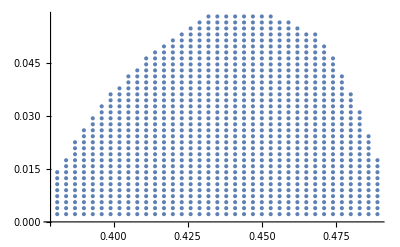

```mathematica
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;

trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,60];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

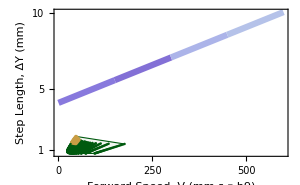

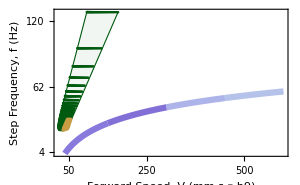

```mathematica
p11=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,10},{0,250,500},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p12=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{4,62,120},{50,250,500},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

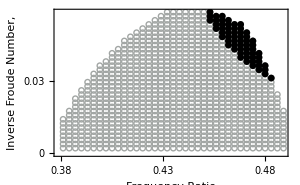

```mathematica
ppoints=ϕγU[[positionCNF]];
p13=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number,",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0.38,0.43,0.48}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
result11
```

{0.00838051,0.0137477}

{0.144756,0.30849}

{{{0.468,0.0532},{0.471,0.0498},{0.468,0.0515},{0.474,0.0464},{0.471,0.0481},{0.465,0.0532},{0.468,0.0498},{0.474,0.0447},{0.462,0.0549},{0.465,0.0515},{0.471,0.0464},{0.477,0.0413},{0.468,0.0481},{0.459,0.0566},{0.474,0.043},{0.462,0.0532},{0.465,0.0498},{0.471,0.0447},{0.468,0.0464},{0.477,0.0396},{0.459,0.0549},{0.462,0.0515},{0.474,0.0413},{0.465,0.0481},{0.471,0.043},{0.459,0.0532},{0.48,0.0362},{0.468,0.0447},{0.462,0.0498},{0.477,0.0379},{0.456,0.0566},{0.474,0.0396},{0.465,0.0464},{0.471,0.0413},{0.459,0.0515},{0.456,0.0549},{0.468,0.043},{0.462,0.0481},{0.48,0.0345},{0.477,0.0362},{0.465,0.0447},{0.474,0.0379},{0.453,0.0583},{0.471,0.0396},{0.459,0.0498},{0.456,0.0532},{0.462,0.0464},{0.468,0.0413},{0.453,0.0566},{0.465,0.043},{0.48,0.0328},{0.483,0.0311},{0.477,0.0345},{0.456,0.0515},{0.474,0.0362},{0.459,0.0481},{0.471,0.0379},{0.453,0.0549},{0.462,0.0447},{0.468,0.0396}},{35.3319,55.1007},{23.6664,33.2881},{35.3319,55.1007},{1.44557,1.87332},{253.145,5869.17},{58.873,67.4715}}

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

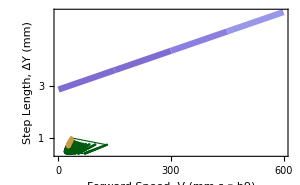

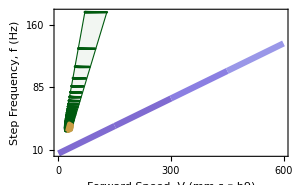

```mathematica
p14=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,3,6},{0,300,600},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p15=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,85,160},{0,300,600},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

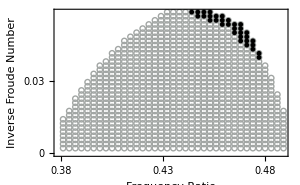

```mathematica
ppoints=ϕγU[[positionCNF]];

p16=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0.38,0.43,0.48}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.00645548,0.0137477}

{0.18067,0.306994}

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
```

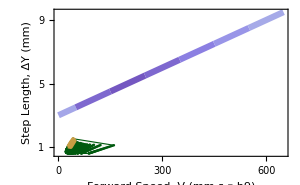

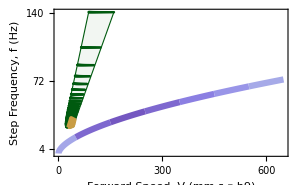

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,30];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p17=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,300,600},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p18=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{4,72,140},{0,300,600},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

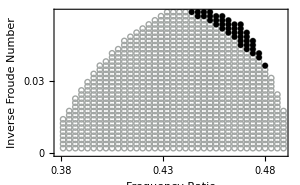

```mathematica
ppoints=ϕγU[[positionCNF]];

p19=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0.38,0.43,0.48}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.00645548,0.0137477}

{0.0491062,0.0924299}

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*)/10;
speedstride = Transpose[{speedD (*mm to cm*), steplengthD}];
speedFreq = Transpose[{speedD(*mm to cm*), freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,25];
```

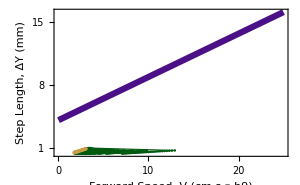

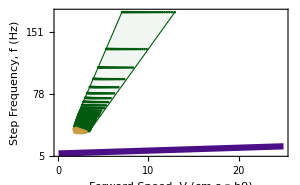

```mathematica
p110=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{1,8,15},{0,10,20},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p111=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,78,151},{0,10,20},formicaPolyctenaFreq,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

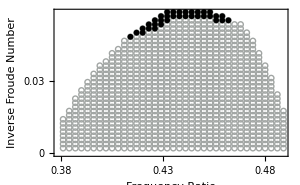

```mathematica
ppoints=ϕγU[[positionCNF]];

p112=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0.38,0.43,0.48}],Automatic}},ImageSize->{300,260}]
]
```

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

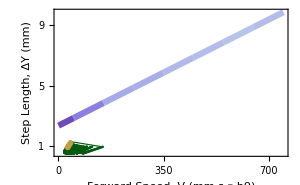

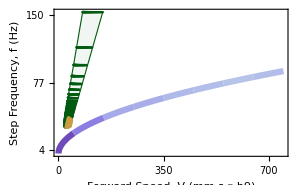

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,40];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p113=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,350,700},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p114=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{4,77,150},{0,350,700},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

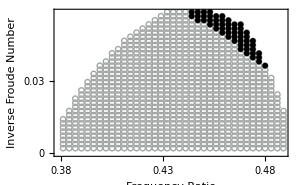

```mathematica
ppoints=ϕγU[[positionCNF]];

p115=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0.38,0.43,0.48}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.00642944,0.0137477}

{0.138341,0.260393}

## Grid Search Y2 Ratio1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY2.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY2points.mx"];
```

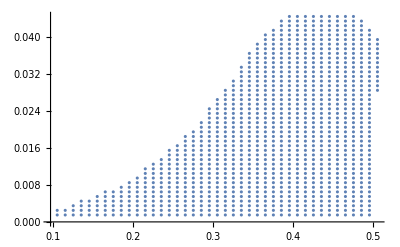

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;

trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,40];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

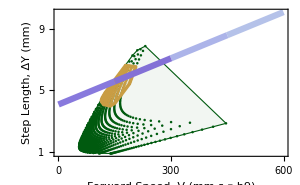

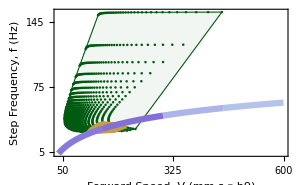

```mathematica
p21=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,300,600},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p22=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,75,145},{50,325,600},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

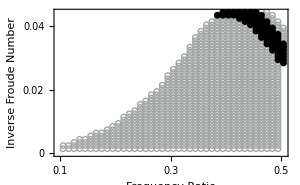

```mathematica
ppoints=ϕγU[[positionCNF]];
p23=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0666273,0.172593}

{0.140897,0.370005}

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

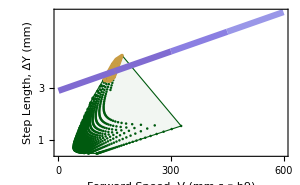

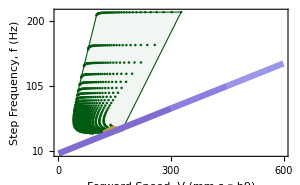

```mathematica
p24=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,3,6},{0,300,600},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p25=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,105,200},{0,300,600},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

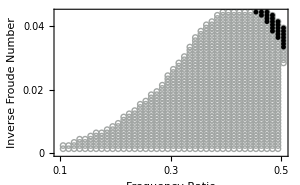

```mathematica
ppoints=ϕγU[[positionCNF]];

p26=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.140622,0.245893}

{0.249927,0.408967}

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
```

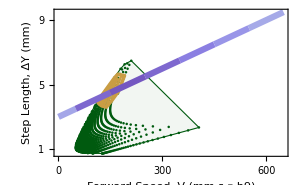

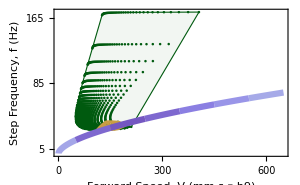

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,30];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p27=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,300,600},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p28=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,85,165},{0,300,600},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

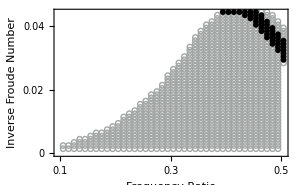

```mathematica
ppoints=ϕγU[[positionCNF]];

p29=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.079644,0.184261}

{0.0511959,0.12623}

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND/10(*in cm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,25];
```

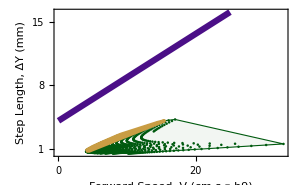

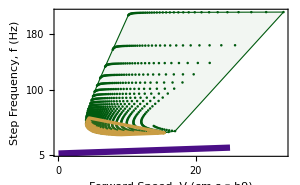

```mathematica
p210=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{1,8,15},{0,20,40},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p211=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,100,180},{0,20,40},formicaPolyctenaFreq,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

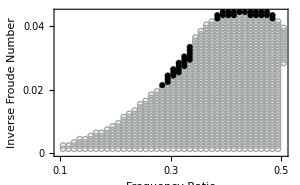

```mathematica
ppoints=ϕγU[[positionCNF]];

p212=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
]
```

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

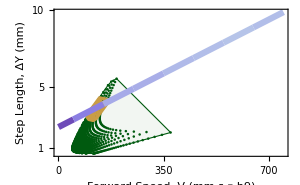

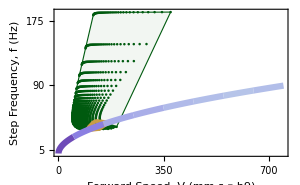

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,40];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p213=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,10},{0,350,700},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p214=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,90,175},{0,350,700},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

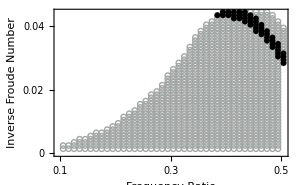

```mathematica
ppoints=ϕγU[[positionCNF]];

p215=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0666273,0.143716}

{0.140168,0.368091}

## Grid Search Y3 Ratio1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY3.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY3points.mx"];
```

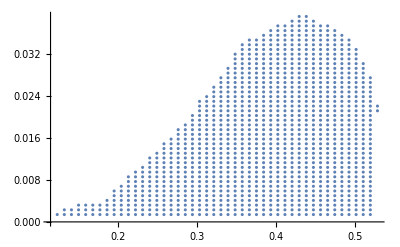

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;

trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,60];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

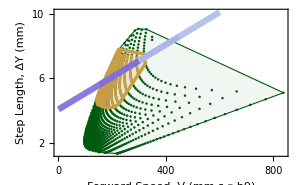

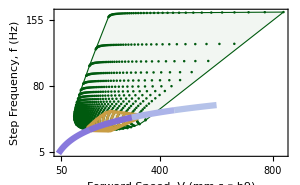

```mathematica
p31=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,6,10},{0,400,800},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p32=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,80,155},{50,400,800},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

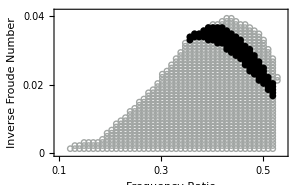

```mathematica
ppoints=ϕγU[[positionCNF]];
p33=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260},PlotRange->{{0.1,0.54},{0,0.041}}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0814307,0.247258}

{0.159013,0.680189}

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

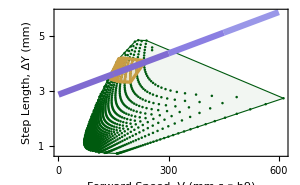

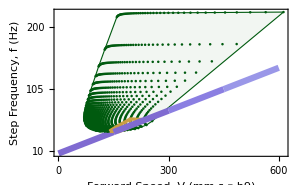

```mathematica
p34=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,3,5},{0,300,600},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p35=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,105,200},{0,300,600},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

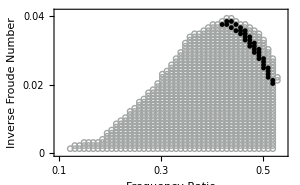

```mathematica
ppoints=ϕγU[[positionCNF]];

p36=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260},PlotRange->{{0.1,0.54},{0,0.041}}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.166595,0.258775}

{0.258416,0.726994}

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
```

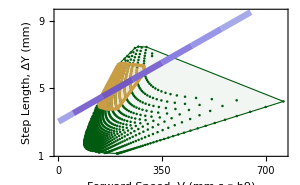

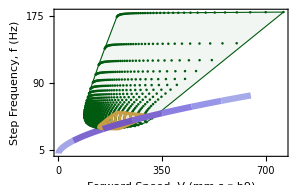

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,30];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p37=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,350,700},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p38=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,90,175},{0,350,700},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

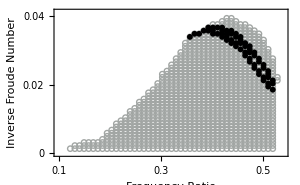

```mathematica
ppoints=ϕγU[[positionCNF]];

p39=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260},PlotRange->{{0.1,0.54},{0,0.041}}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0930839,0.257508}

{0.0561517,0.216823}

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*)/10;
speedstride = Transpose[{speedD(*mm to cm*), steplengthD}];
speedFreq = Transpose[{speedD(*mm to cm*), freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,25];
```

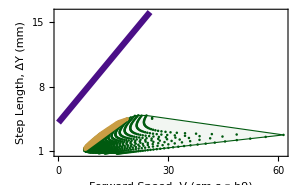

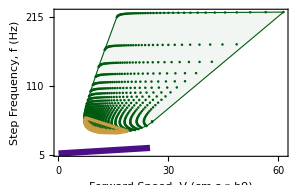

```mathematica
p310=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{1,8,15},{0,30,60},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p311=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,110,215},{0,30,60},formicaPolyctenaFreq,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

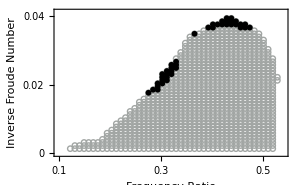

```mathematica
ppoints=ϕγU[[positionCNF]];

p312=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260},PlotRange->{{0.1,0.54},{0,0.041}}]
]
```

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

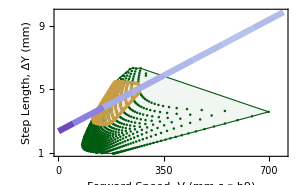

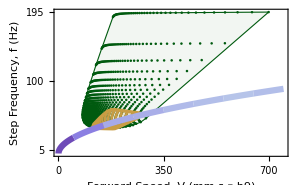

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p313=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,5,9},{0,350,700},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p314=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,100,195},{0,350,700},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

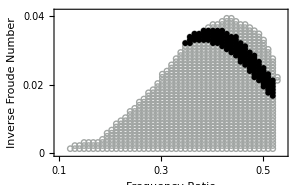

```mathematica
ppoints=ϕγU[[positionCNF]];

p315=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.02,0.04}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260},PlotRange->{{0.1,0.54},{0,0.041}}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0732309,0.257508}

{0.15819,0.676671}

## Grid Search Y4 Ratio1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY4.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY4points.mx"];
```

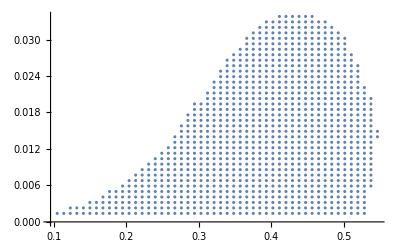

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;

grf=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\GRFY4.mx"];
cot=engC/steplength;

trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
ampD=amp*hmeanD;

energyD=(20* 10^-6*(hmeanD/1000)^2*freqD^2)engC*10^6(*In micro joules*);
cotD=((hmeanD/1000)*freqD^2)cot(*N/(kg m)*);

grfD=20*10^-6*hmeanD*omega0^2*grf (*Newton*);
```

```mathematica
hmeanD
```

3.64428

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

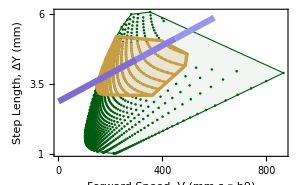

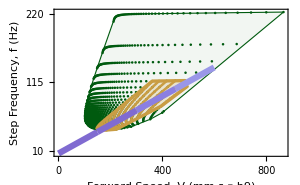

```mathematica
p44=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{1,3.5,6},{0,400,800},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p45=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,115,220},{0,400,800},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

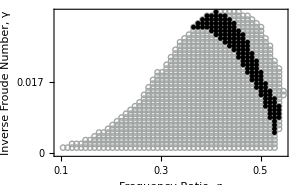

```mathematica
ppoints=ϕγU[[positionCNF]];

p46=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},FrameTicks->{{tiksfunc[{0,0.017,0.035}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[omega0[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[speedD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[(freqD*stepFreq)[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[steplengthD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[ampD[[funcCommonPos[positionCNF,stiff,eff]]]]

MinMax[cotD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[energyD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[grfD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[perCong[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{109.216,387.219}

{0.238561,2.99877}

{147.912,495.514}

{41.6282,117.512}

{0.14827,0.380939}

{3.09637,5.19886}

{0.958162,1.96642}

{1275.14,13865.9}

{131.549,904.514}

{1.90026,25.2116}

{48.6644,50.474}

FittedModel[…]

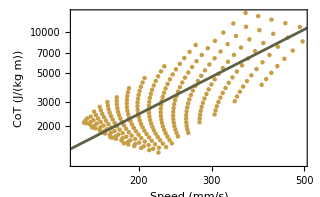

```mathematica
speedCOT=Transpose[{speedD[[funcCommonPos[positionCNF,stiff,eff]]],cotD[[funcCommonPos[positionCNF,stiff,eff]]]}];
fit=NonlinearModelFit[speedCOT,a x^b,{a,b},x]
cot2=Show[ListPlot[speedCOT,PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},FrameLabel->{{"CoT (J/(kg m))",None},{"Speed (mm/s)",None}},PlotStyle->{ColorData["FruitPunchColors",0.5],PointSize[0.01]}],
Plot[fit[x],{x,0,700},Filling->{2->{1}},ScalingFunctions->{"Log","Log"},PlotStyle->ColorData["FallColors",0.2]],ImageSize->{320,200}
]
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*it is l max now mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, (freqD*stepFreq)}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
ampD=amp*hmeanD;

energyD=(28.72* 10^-6*(hmeanD/1000)^2*freqD^2)engC*10^6(*In micro joules*);
cotD=((hmeanD/1000)*freqD^2)cot(*N/(kg m)*);

grfD=28.72*10^-6*hmeanD*omega0^2*grf (*Newton*);
```

```mathematica
hmeanD
```

6.79902

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

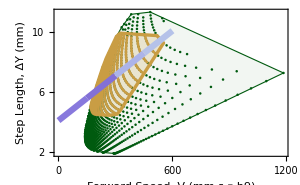

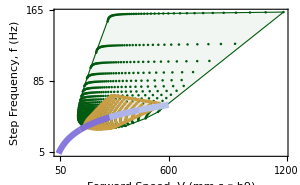

```mathematica
p41=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,6,10},{0,600,1200},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p42=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,85,165},{50,600,1200},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

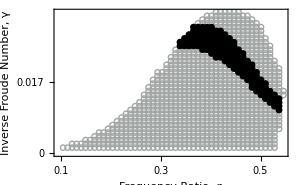

```mathematica
ppoints=ϕγU[[positionCNF]];
p43=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},FrameTicks->{{tiksfunc[{0,0.017,0.035}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[omega0[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[speedD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[(freqD*stepFreq)[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[steplengthD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[ampD[[funcCommonPos[positionCNF,stiff,eff]]]]

MinMax[cotD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[energyD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[grfD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[perCong[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{78.913,199.916}

{0.178847,1.14783}

{169.361,553.025}

{30.4768,68.2901}

{0.0914517,0.406796}

{4.44358,9.92681}

{1.56826,3.61836}

{1275.14,10920.6}

{352.434,1432.55}

{2.61815,18.8455}

{48.7222,50.474}

```mathematica
result11
```

{{{0.492,0.0167},{0.438,0.023},{0.429,0.0239},{0.339,0.0266},{0.447,0.0221},{0.501,0.0158},{0.393,0.0266},{0.483,0.0176},{0.42,0.0248},{0.384,0.0266},{0.402,0.0257},{0.456,0.0212},{0.537,0.0122},{0.51,0.0149},{0.474,0.0185},{0.411,0.0257},{0.519,0.014},{0.528,0.0131},{0.465,0.0203},{0.366,0.0275},{0.357,0.0275},{0.411,0.0248},{0.465,0.0194},{0.375,0.0266},{0.375,0.0275},{0.348,0.0266},{0.474,0.0194},{0.456,0.0203},{0.402,0.0266},{0.42,0.0239},{0.366,0.0266},{0.357,0.0266},{0.447,0.0212},{0.393,0.0257},{0.384,0.0275},{0.429,0.023},{0.438,0.0221},{0.483,0.0185},{0.348,0.0275},{0.438,0.0239},{0.429,0.0248},{0.51,0.014},{0.519,0.0131},{0.447,0.023},{0.501,0.0149},{0.42,0.0257},{0.492,0.0176},{0.393,0.0275},{0.402,0.0248},{0.528,0.0122},{0.492,0.0158},{0.456,0.0221},{0.384,0.0257},{0.411,0.0266},{0.483,0.0167},{0.501,0.0167},{0.465,0.0212},{0.474,0.0176},{0.411,0.0239},{0.537,0.0113},{0.465,0.0185},{0.51,0.0158},{0.375,0.0257},{0.474,0.0203},{0.339,0.0257},{0.42,0.023},{0.456,0.0194},{0.402,0.0275},{0.366,0.0284},{0.375,0.0284},{0.429,0.0221},{0.447,0.0203},{0.438,0.0212},{0.393,0.0248},{0.519,0.0149},{0.366,0.0257},{0.438,0.0248},{0.384,0.0284},{0.483,0.0194},{0.429,0.0257},{0.528,0.014},{0.348,0.0257},{0.537,0.0131},{0.357,0.0284},{0.447,0.0239},{0.357,0.0257},{0.42,0.0266},{0.456,0.023},{0.402,0.0239},{0.492,0.0185},{0.393,0.0284},{0.384,0.0248},{0.411,0.0275},{0.465,0.0221},{0.411,0.023},{0.501,0.014},{0.492,0.0149},{0.501,0.0176},{0.483,0.0158},{0.51,0.0131},{0.375,0.0293},{0.402,0.0284},{0.384,0.0293},{0.366,0.0293},{0.429,0.0266},{0.42,0.0275},{0.438,0.0257},{0.393,0.0293},{0.411,0.0284},{0.447,0.0248},{0.474,0.0212},{0.456,0.0239},{0.402,0.0293},{0.429,0.0275},{0.438,0.0266},{0.465,0.023},{0.42,0.0284},{0.483,0.0203},{0.447,0.0257},{0.384,0.0302},{0.375,0.0302},{0.411,0.0293},{0.474,0.0221},{0.456,0.0248},{0.393,0.0302},{0.366,0.0302},{0.528,0.0113},{0.492,0.0194},{0.537,0.0104},{0.519,0.0122},{0.465,0.0239},{0.402,0.0302},{0.429,0.0284},{0.438,0.0275},{0.51,0.0167},{0.483,0.0212},{0.42,0.0293},{0.447,0.0266}},{169.361,539.565},{32.3255,57.2214},{180.367,553.025},{5.4679,9.59447},{0.00836106,6.50544},{0.0101282,7.4232}}

FittedModel[…]

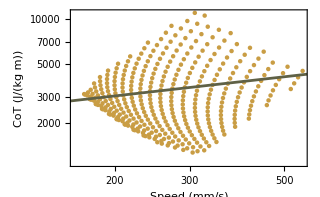

```mathematica
speedCOT=Transpose[{speedD[[funcCommonPos[positionCNF,stiff,eff]]],cotD[[funcCommonPos[positionCNF,stiff,eff]]]}];
fit=NonlinearModelFit[speedCOT,a x^b,{a,b},x]
cot1=Show[ListPlot[speedCOT,PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},FrameLabel->{{"CoT (J/(kg m))",None},{"Speed (mm/s)",None}},PlotStyle->{ColorData["FruitPunchColors",0.5],PointSize[0.01]}],
Plot[fit[x],{x,0,700},Filling->{2->{1}},ScalingFunctions->{"Log","Log"},PlotStyle->ColorData["FallColors",0.2]],ImageSize->{320,200}
]
```

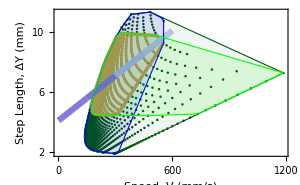

```mathematica
Show[p41,
HighlightMesh[ConvexHullMesh[funcCNF[positionCNF,stiff,speedstride]],{Style[2,Blue,Opacity[0.1]],Style[1,Blue,Opacity[1]]}],
HighlightMesh[ConvexHullMesh[funcCNF[positionCNF,eff,speedstride]],{Style[2,Green,Opacity[0.1]],Style[1,Green,Opacity[1]]}]
]
```

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
ampD=amp*hmeanD;

energyD=(20* 10^-6*(hmeanD/1000)^2*freqD^2)engC*10^6(*In micro joules*);
cotD=((hmeanD/1000)*freqD^2)cot(*N/(kg m)*);

grfD=20*10^-6*hmeanD*omega0^2*grf (*Newton*);
```

```mathematica
hmeanD
```

4.75932

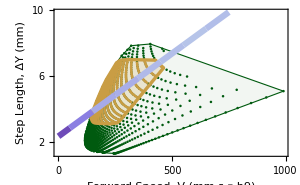

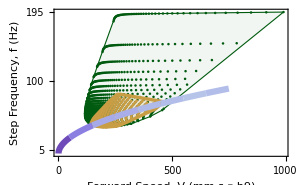

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,120];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p413=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,6,10},{0,500,1000},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p414=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,100,195},{0,500,1000},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

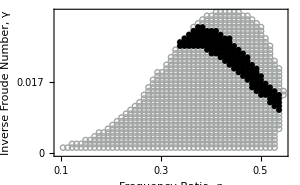

```mathematica
ppoints=ϕγU[[positionCNF]];

p415=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},FrameTicks->{{tiksfunc[{0,0.017,0.035}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[omega0[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[speedD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[(freqD*stepFreq)[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[steplengthD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[ampD[[funcCommonPos[positionCNF,stiff,eff]]]]

MinMax[cotD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[energyD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[grfD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[perCong[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{94.3191,238.945}

{0.177922,1.1419}

{141.698,462.694}

{36.4268,81.6223}

{0.0914517,0.420606}

{3.11051,6.99496}

{1.09778,2.53285}

{1275.14,10920.6}

{171.799,698.316}

{1.82322,13.1236}

{48.7222,50.474}

FittedModel[…]

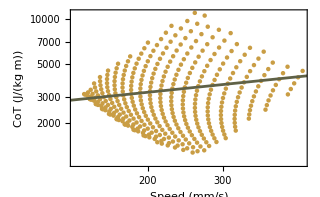

```mathematica
speedCOT=Transpose[{speedD[[funcCommonPos[positionCNF,stiff,eff]]],cotD[[funcCommonPos[positionCNF,stiff,eff]]]}];
fit=NonlinearModelFit[speedCOT,a x^b,{a,b},x]
cot4=Show[ListPlot[speedCOT,PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},FrameLabel->{{"CoT (J/(kg m))",None},{"Speed (mm/s)",None}},PlotStyle->{ColorData["FruitPunchColors",0.5],PointSize[0.01]}],
Plot[fit[x],{x,0,700},Filling->{2->{1}},ScalingFunctions->{"Log","Log"},PlotStyle->ColorData["FallColors",0.2]],ImageSize->{320,200}
]
```

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
ampD=amp*hmeanD;

energyD=(8.367* 10^-6*(hmeanD/1000)^2*freqD^2)engC*10^6(*In micro joules*);
cotD=((hmeanD/1000)*freqD^2)cot(*N/(kg m)*);

grfD=8.367*10^-6*hmeanD*omega0^2*grf (*Newton*);
```

```mathematica
hmeanD
```

5.60919

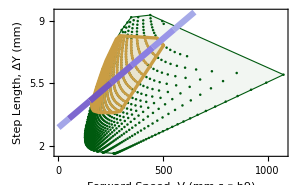

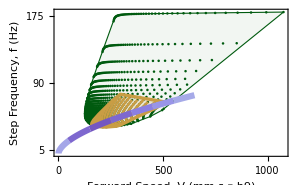

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p47=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,5.5,9},{0,500,1000},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p48=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,90,175},{0,500,1000},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

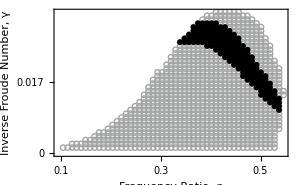

```mathematica
ppoints=ϕγU[[positionCNF]];

p49=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},FrameTicks->{{tiksfunc[{0,0.017,0.035}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[omega0[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[speedD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[(freqD*stepFreq)[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[steplengthD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[ampD[[funcCommonPos[positionCNF,stiff,eff]]]]

MinMax[cotD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[energyD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[grfD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[perCong[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{86.8804,220.1}

{0.0631558,0.405332}

{158.592,502.31}

{33.5539,75.1849}

{0.0993387,0.406796}

{3.85301,8.18962}

{1.29399,2.98515}

{1275.14,10470.6}

{84.7065,344.308}

{0.762745,5.49026}

{48.7222,50.474}

FittedModel[…]

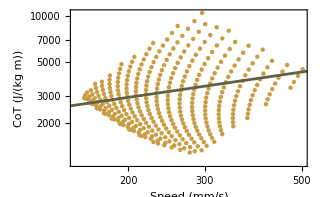

```mathematica
speedCOT=Transpose[{speedD[[funcCommonPos[positionCNF,stiff,eff]]],cotD[[funcCommonPos[positionCNF,stiff,eff]]]}];
fit=NonlinearModelFit[speedCOT,a x^b,{a,b},x]
cot3=Show[ListPlot[speedCOT,PlotRange->All,ScalingFunctions->{"Log","Log"},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},FrameLabel->{{"CoT (J/(kg m))",None},{"Speed (mm/s)",None}},PlotStyle->{ColorData["FruitPunchColors",0.5],PointSize[0.01]}],
Plot[fit[x],{x,0,700},Filling->{2->{1}},ScalingFunctions->{"Log","Log"},PlotStyle->ColorData["FallColors",0.2]],ImageSize->{320,200}
]
```

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in cmmm/sec*)/10;
speedstride = Transpose[{speedD (*mm to cm*), steplengthD}];
speedFreq = Transpose[{speedD(*mm to cm*), freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
ampD=amp*hmeanD;

energyD=(21.77* 10^-6*(hmeanD/1000)^2*freqD^2)engC*10^6(*In micro joules*);
cotD=((hmeanD/1000)*freqD^2)cot(*N/(kg m)*);

grfD=21.77*10^-6*hmeanD*omega0^2*grf (*Newton*);
```

```mathematica
hmeanD
```

3.66467

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,25];
```

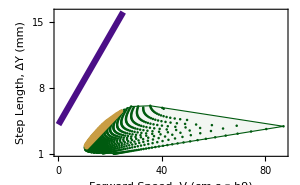

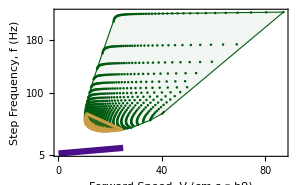

```mathematica
p410=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{1,8,15},{0,40,80},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p411=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,100,180},{0,40,80},0.34 t +7.6,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

```mathematica
MinMax[omega0[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[speedD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[(freqD*stepFreq)[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[steplengthD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[ampD[[funcCommonPos[positionCNF,stiff,eff]]]]

MinMax[cotD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[energyD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[grfD[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[perCong[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{109.155,137.025}

{0.259383,0.408748}

{10.2385,24.4097}

{41.5122,67.6567}

{0.0409264,0.431735}

{1.61898,5.56202}

{0.549988,1.46803}

{1240.64,8981.83}

{143.993,316.567}

{1.96783,3.37467}

{49.5524,50.474}

{{0.456,0.0338},{0.411,0.0338},{0.447,0.0338},{0.42,0.0338},{0.438,0.0338},{0.429,0.0338},{0.474,0.0329},{0.393,0.0329},{0.465,0.0329},{0.402,0.0329},{0.456,0.0329},{0.411,0.0329},{0.447,0.0329},{0.438,0.0329},{0.42,0.0329},{0.429,0.0329},{0.384,0.032},{0.474,0.032},{0.294,0.0194},{0.285,0.0176},{0.294,0.0185},{0.312,0.0212},{0.303,0.0194},{0.312,0.0203},{0.321,0.023},{0.321,0.0221},{0.294,0.0176},{0.303,0.0185},{0.285,0.0167},{0.321,0.0212},{0.276,0.0158},{0.312,0.0194},{0.33,0.023},{0.33,0.0239},{0.321,0.0203},{0.33,0.0221},{0.303,0.0176},{0.294,0.0167}}

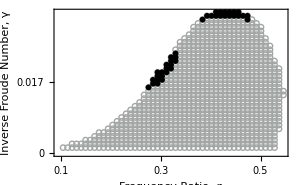

```mathematica
ppoints=ϕγU[[positionCNF]]
p412=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Roman 10"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number, γ",None},{"Frequency Ratio, φ",None}},FrameTicks->{{tiksfunc[{0,0.017,0.035}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
]
```

```mathematica
result11
```

{{{0.456,0.0338},{0.411,0.0338},{0.447,0.0338},{0.42,0.0338},{0.438,0.0338},{0.429,0.0338},{0.474,0.0329},{0.393,0.0329},{0.465,0.0329},{0.402,0.0329},{0.456,0.0329},{0.483,0.032},{0.411,0.0329},{0.447,0.0329},{0.438,0.0329},{0.42,0.0329},{0.429,0.0329},{0.384,0.032},{0.474,0.032},{0.492,0.0311},{0.294,0.0194},{0.285,0.0176},{0.294,0.0185},{0.312,0.0212},{0.303,0.0194},{0.312,0.0203},{0.321,0.023},{0.321,0.0221},{0.294,0.0176},{0.303,0.0185},{0.285,0.0167},{0.321,0.0212},{0.276,0.0158},{0.312,0.0194},{0.33,0.023},{0.33,0.0239},{0.321,0.0203},{0.33,0.0221},{0.303,0.0176},{0.294,0.0167}},{16.2423,26.6495},{41.5122,45.6555},{10.2385,11.7949},{1.73712,2.46417},{174.029,219.409},{74.7564,80.7297}}

## Grid Search Y5 Ratio1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY5.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY5points.mx"];
```

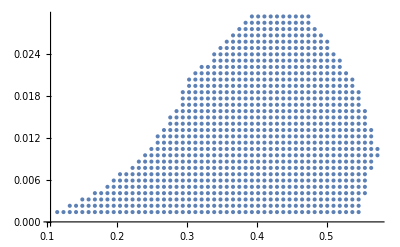

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;


trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,60];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

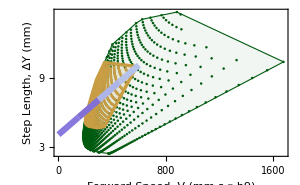

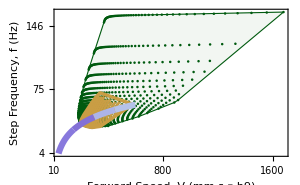

```mathematica
p51=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{3,9,15},{0,800,1600},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p52=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{4,75,146},{10,800,1600},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

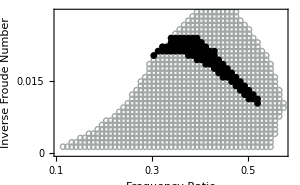

```mathematica
ppoints=ϕγU[[positionCNF]];
p53=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.015,0.03}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0992334,0.408516}

{0.181215,1.03778}

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,70];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

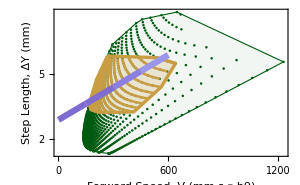

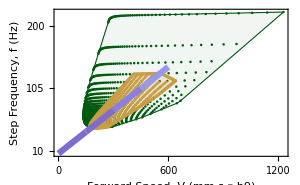

```mathematica
p54=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,5,8},{0,600,1200},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p55=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,105,200},{0,600,1200},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

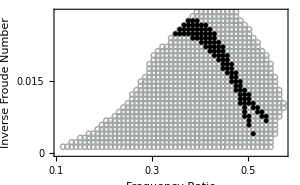

```mathematica
ppoints=ϕγU[[positionCNF]];

p56=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.015,0.03}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.155989,0.468402}

{0.254209,3.30249}

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
```

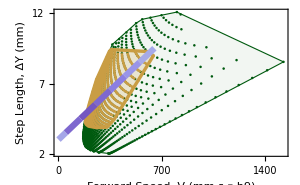

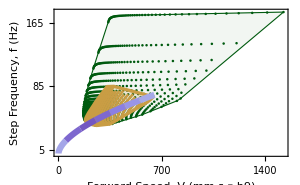

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p57=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,7,12},{0,700,1400},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p58=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,85,165},{0,700,1400},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

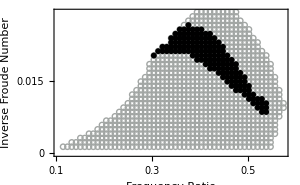

```mathematica
ppoints=ϕγU[[positionCNF]];

p59=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.015,0.03}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0992334,0.512222}

{0.0639919,0.474445}

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in cmm/sec*)/10;
speedstride = Transpose[{speedD (*mm to cm*), steplengthD}];
speedFreq = Transpose[{speedD(*mm to cm*), freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,25];
```

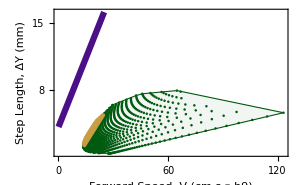

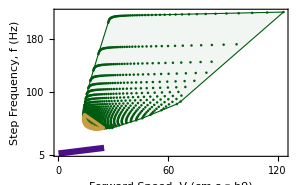

```mathematica
p510=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{1,8,15},{0,60,120},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p511=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,100,180},{0,60,120},0.34 t +7.6,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

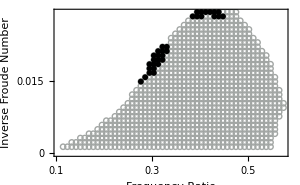

```mathematica
ppoints=ϕγU[[positionCNF]];
p512=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.015,0.03}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
]
```

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

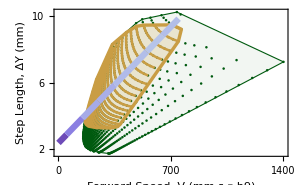

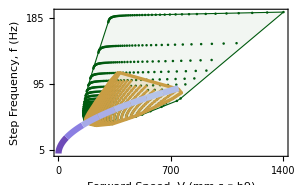

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p513=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{2,6,10},{0,700,1400},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p514=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,95,185},{0,700,1400},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

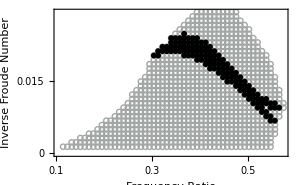

```mathematica
ppoints=ϕγU[[positionCNF]];

p515=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.015,0.03}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.0992334,0.733531}

{0.180277,1.80563}

## Grid Search Y8 Ratio 1.5

```mathematica
results=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY8.mx"];
points=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\Feasible Region Charactersitics\\ForAntY8points.mx"];
```

```mathematica
resultsU=filterPoints[results,points][[1]];
ϕγU=filterPoints[results,points][[2]];
ϕγUL(*updated length*)=filterPoints[results,points][[3]];
```

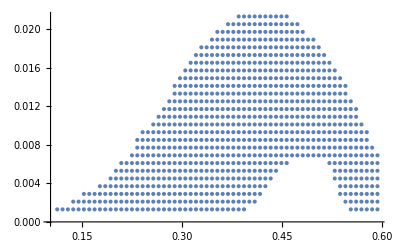

```mathematica
ListPlot[ϕγU]
```

```mathematica
convergP=Table[resultsU[[i,2]],{i,1,ϕγUL}];
steplength=Table[resultsU[[i,1,2,1]],{i,1,ϕγUL}];
speedND=Table[resultsU[[i,1,2,2]],{i,1,ϕγUL}];
stepFreq=Table[resultsU[[i,1,2,3]],{i,1,ϕγUL}];
perCong=Table[resultsU[[i,3,1]],{i,1,ϕγUL}];
amp=Table[resultsU[[i,3,2]],{i,1,ϕγUL}];
engC=Table[resultsU[[i,3,3]],{i,1,ϕγUL}];
meanh=Table[resultsU[[i,3,4]],{i,1,ϕγUL}];
eff=(0.5 speedND^2/engC)*100;


trilength=Table[Sqrt[(resultsU[[i,1,1,2]]-resultsU[[i,1,1,1]])^2+(resultsU[[i,1,1,3]])^2],{i,1,ϕγUL}];
```

### Cataglyphis bicolor

```mathematica
hmean = 10(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=28.72 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBicolorFreq,cataglyphisBicolorStride,50];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

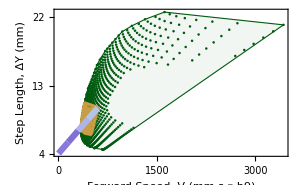

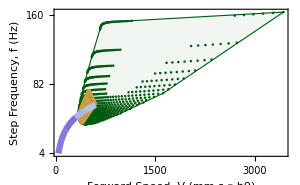

```mathematica
p81=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{4,13,22},{0,1500,3000},cataglyphisBicolorStride,"0.02x + 8.18",{1200,12},{t,0,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],
breakplots[cataglyphisBicolorStride,{0,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
p82=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{4,82,160},{0,1500,3000},cataglyphisBicolorFreq,"10.16 Log(x) - 36.02",{1200,22},{t,40,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBicolorFreq,{40,150,300,450,600},{0.63,0.66,0.35,0.28}]
]
```

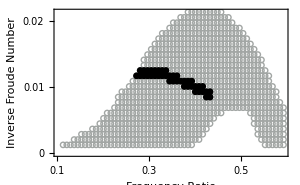

```mathematica
ppoints=ϕγU[[positionCNF]];
p83=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",7}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.01,0.02}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.15396,0.339672}

{0.217689,0.760134}

### C . Albicans

```mathematica
hmean = 5.36(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisAlbicansFreq,cataglyphisAlbicansStride,70];
positionCNF=cleanpoint[ϕγU,result11,speedD,600];
```

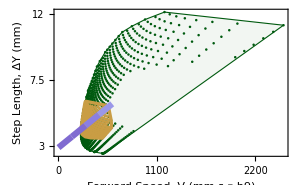

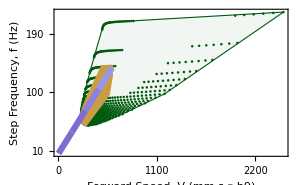

```mathematica
p84=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{3,7.5,12},{0,1100,2200},cataglyphisAlbicansStride,"0.01x+5.75",{800,6},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[cataglyphisAlbicansStride,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
p85=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{10,100,190},{0,1100,2200},cataglyphisAlbicansFreq,"0.11x+2.85",{380,30},{t,10,600}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisAlbicansFreq,{0,150,300,450,600},{0.68,0.68,0.61,0.50}]
]
```

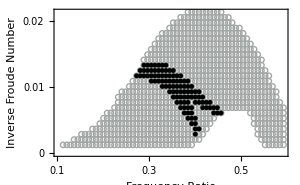

```mathematica
ppoints=ϕγU[[positionCNF]];

p86=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,18,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",5}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.01,0.02}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.15396,0.374104}

{0.281163,2.48259}

### C . Fortis

```mathematica
hmean = 8.25(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=8.367 10^-6 omega0^2;
```

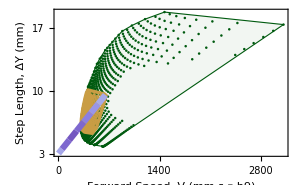

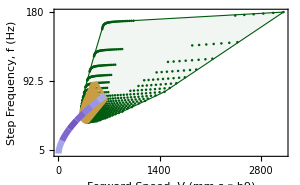

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisFortisFreq,cataglyphisFortisStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,650];

p87=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{3,10,17},{0,1400,2800},cataglyphisFortisStride,"0.02x+6.04",{1000,9},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisFortisStride,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]

]
p88=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,92.5,180},{0,1400,2800},cataglyphisFortisFreq,"0.81x^0.59",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],linesInsideRegfunc[speedFreq],
breakplots[cataglyphisFortisFreq,{0,50,150,250,350,450,550,650},{0.42,0.69,0.75,0.69,0.61,0.51,0.4}]
]
```

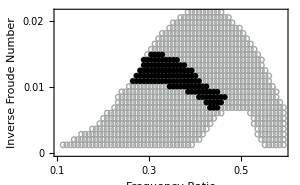

```mathematica
ppoints=ϕγU[[positionCNF]];

p89=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.01,0.02}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.144272,0.435986}

{0.0720844,0.355556}

### F . Polyctena

```mathematica
hmean = 5.39(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in cmm/sec*)/10;
speedstride = Transpose[{speedD(*mm to cm*), steplengthD}];
speedFreq = Transpose[{speedD(*mm to cm*), freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=21.77 10^-6 omega0^2;
```

```mathematica
result11=closedranges[speedFreq,speedstride,formicaPolyctenaFreq,formicaPolyctenaStride,20];
positionCNF=cleanpoint[ϕγU,result11,speedD,60];
```

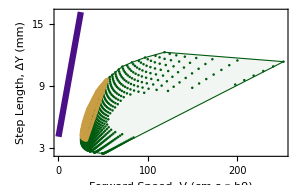

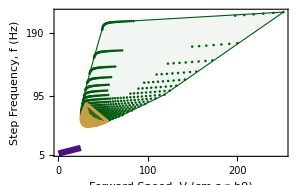

```mathematica
p810=Show[plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (cm s ⁻.b9)",{3,9,15},{0,100,200},formicaPolyctenaStride,"0.48x+4.1",{60,12},{t,1,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],
linesInsideRegfunc[speedstride],
breakplots[formicaPolyctenaStride,{0,25},{1}]
]
p811=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (cm s ⁻.b9)",{5,95,190},{0,100,200},0.34 t +7.6,"0.34x+7.6",{80,30},{t,0,25}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[formicaPolyctenaFreq,{0,25},{1}]
]
```

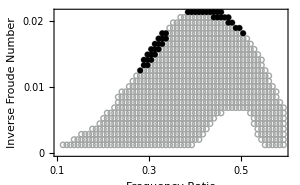

```mathematica
ppoints=ϕγU[[positionCNF]];

p812=Show[ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.01,0.02}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.164601,0.949395}

{0.28691,0.682846}

### C . bombycina

```mathematica
hmean =7(*mm*);
hmeanD = (1/Max[trilength])*hmean;
steplengthD = hmeanD*steplength;
gamma = Map[#[[2]] &, ϕγU];
freqD = Sqrt[9.8/(gamma*(hmeanD/1000(*mm to m*)))];
speedD = hmeanD*freqD*speedND(*in mm/sec*);
speedstride = Transpose[{speedD, steplengthD}];
speedFreq = Transpose[{speedD, freqD*stepFreq}];
omega0=freqD*Map[#[[1]]&, ϕγU];
stiff=20 10^-6 omega0^2;
```

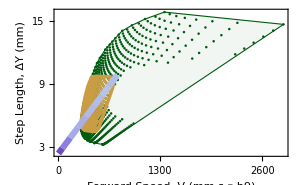

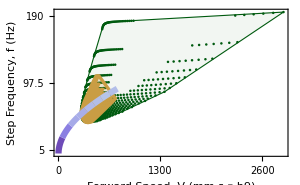

```mathematica
result11=closedranges[speedFreq,speedstride,cataglyphisBombycinaFreq,cataglyphisBombycinaStride,100];
positionCNF=cleanpoint[ϕγU,result11,speedD,750];

p813=Show[
plotfunc[speedstride,"Step Length, ΔY (mm)","Forward Speed, V (mm s ⁻.b9)",{3,9,15},{0,1300,2600},cataglyphisBombycinaStride,"",{1000,9},{t,10,750}],
commonregionplotfunc[positionCNF,stiff,eff,speedstride],linesInsideRegfunc[speedstride],breakplots[cataglyphisBombycinaStride,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]

]
p814=Show[plotfunc[speedFreq,"Step Frequency, f (Hz)","Forward Speed, V (mm s ⁻.b9)",{5,97.5,190},{0,1300,2600},cataglyphisBombycinaFreq,"",{1100,30},{t,10,650}],
commonregionplotfunc[positionCNF,stiff,eff,speedFreq],
linesInsideRegfunc[speedFreq],
breakplots[cataglyphisBombycinaFreq,{0,50,150,250,350,450,550,650,750},{0.79,0.61,0.4,0.38,0.32,0.30,0.27,0.3}]
]
```

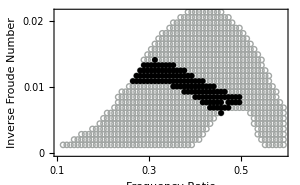

```mathematica
ppoints=ϕγU[[positionCNF]];

p815=ListPlot[{ϕγU,ppoints},PlotStyle->{{ColorData["GrayTones",0.7],PointSize->0.0001},{Black,PointSize->0.007}},Frame->True,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"},PlotMarkers->{{"○",5.5},{"●",6}},FrameLabel->{{"Inverse Froude Number",None},{"Frequency Ratio",None}},FrameTicks->{{tiksfunc[{0,0.01,0.02}],Automatic},{tiksfunc[{0.1,0.3,0.5}],Automatic}},ImageSize->{300,260}]
```

```mathematica
MinMax[eff[[funcCommonPos[positionCNF,stiff,eff]]]]
MinMax[stiff[[funcCommonPos[positionCNF,stiff,eff]]]]
```

{0.144272,0.59663}

{0.21529,1.17377}

## Combine Plots

```mathematica
Needs["MaTeX`"]
```

```mathematica
dummygraphic=Graphics[{},ImageSize->{5,100}];
```

```mathematica
plot1=Show[GraphicsGrid[{{p47,p48,dummygraphic,p49},{p413,p414,dummygraphic,p415}},ImageSize->{990,550},Spacings->{Scaled[0],Scaled[-0.2]}],
Graphics[{Text[Style["a",White,18,FontFamily->"Latin Modern Math"],{30,30}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{30,5}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{330,5}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{620,5}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{30,-220}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{330,-220}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{620,-220}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fortis}"],Pi/2],18,FontFamily->"Latin Modern Math"],{0,-105}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18,FontFamily->"Latin Modern Math"],{0,-325}]

}]
]
```

-Graphics-

```mathematica
plot1F=Overlay[{plot1,
Graphics[Inset[legentripod,Scaled[{-0.28,1}]],ImageSize->{900,520}],
Graphics[Inset[legend2,Scaled[{0.50,0.955}]],ImageSize->{900,500}],
Graphics[Inset[legend1,Scaled[{0.76,0.955}]],ImageSize->{900,500}]

}]
```

-Graphics--Graphics--Graphics--Graphics-

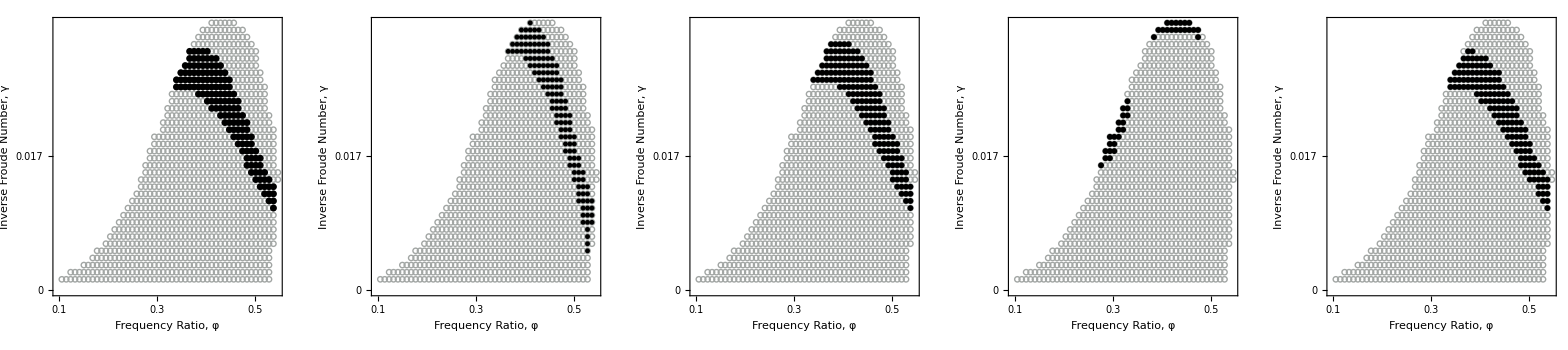

```mathematica
plot3=Show[GraphicsGrid[{{p43,p46,p49,p412,p415}},ImageSize->{1600,350}],
Graphics[{Text[Style["a",18,FontFamily->"Latin Modern Math"],{20,0}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{345,0}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{670,0}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{990,0}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{1320,0}]

}]
]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\comp2DA.pdf",plot1F]
(*Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\comp2DB.pdf",plot3]*)
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\comp2DA.pdf

```mathematica
pall1=Show[GraphicsGrid[{{p24,p34,p44,p54,p84},{p21,p31,p41,p51,p81},{p213,p313,p413,p513,p813},{p27,p37,p47,p57,p87},{p210,p310,p410,p510,p810}},ImageSize->{1580,1330},Spacings->{Scaled[0],Scaled[0]}],

Graphics[{Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. albicans}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-110}],
Text[Style[Rotate[MaTeX[ "\\LARGE \\textit{C. bicolor}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-370}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-630}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fortis}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-890}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{F. polyctena}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-1150}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{10,0}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{310,0}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{610,0}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{910,0}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{1210,0}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{10,-250}],
Text[Style["g",18,FontFamily->"Latin Modern Math"],{310,-250}],
Text[Style["h",18,FontFamily->"Latin Modern Math"],{610,-250}],
Text[Style["i",18,FontFamily->"Latin Modern Math"],{910,-250}],
Text[Style["j",18,FontFamily->"Latin Modern Math"],{1210,-250}],
Text[Style["k",18,FontFamily->"Latin Modern Math"],{10,-520}],
Text[Style["l",18,FontFamily->"Latin Modern Math"],{310,-520}],
Text[Style["m",18,FontFamily->"Latin Modern Math"],{610,-520}],
Text[Style["n",18,FontFamily->"Latin Modern Math"],{910,-520}],
Text[Style["o",18,FontFamily->"Latin Modern Math"],{1210,-520}],
Text[Style["p",18,FontFamily->"Latin Modern Math"],{10,-770}],
Text[Style["q",18,FontFamily->"Latin Modern Math"],{310,-770}],
Text[Style["r",18,FontFamily->"Latin Modern Math"],{610,-770}],
Text[Style["s",18,FontFamily->"Latin Modern Math"],{910,-770}],
Text[Style["t",18,FontFamily->"Latin Modern Math"],{1210,-770}],
Text[Style["u",18,FontFamily->"Latin Modern Math"],{10,-1030}],
Text[Style["v",18,FontFamily->"Latin Modern Math"],{310,-1030}],
Text[Style["w",18,FontFamily->"Latin Modern Math"],{610,-1030}],
Text[Style["x",18,FontFamily->"Latin Modern Math"],{910,-1030}],
Text[Style["y",18,FontFamily->"Latin Modern Math"],{1210,-1030}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.02$}"],18,FontFamily->"Latin Modern Math"],{160,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.03$}"],18,FontFamily->"Latin Modern Math"],{470,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.04$}"],18,FontFamily->"Latin Modern Math"],{770,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.05$}"],18,FontFamily->"Latin Modern Math"],{1060,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.08$}"],18,FontFamily->"Latin Modern Math"],{1360,0}]

}]

]
```

-Graphics-

```mathematica
pa112=Show[GraphicsGrid[{{p25,p35,p45,p55,p85},{p22,p32,p42,p52,p82},{p214,p314,p414,p514,p814},{p28,p38,p48,p58,p88},{p211,p311,p411,p511,p811}},ImageSize->{1600,1350},Spacings->{Scaled[0],Scaled[0]}],

Graphics[{Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. albicans}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-110}],
Text[Style[Rotate[MaTeX[ "\\LARGE \\textit{C. bicolor}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-370}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-630}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fortis}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-890}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{F. polyctena}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-1150}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{10,0}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{310,0}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{610,0}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{910,0}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{1210,0}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{10,-250}],
Text[Style["g",18,FontFamily->"Latin Modern Math"],{310,-250}],
Text[Style["h",18,FontFamily->"Latin Modern Math"],{610,-250}],
Text[Style["i",18,FontFamily->"Latin Modern Math"],{910,-250}],
Text[Style["j",18,FontFamily->"Latin Modern Math"],{1210,-250}],
Text[Style["k",18,FontFamily->"Latin Modern Math"],{10,-520}],
Text[Style["l",18,FontFamily->"Latin Modern Math"],{310,-520}],
Text[Style["m",18,FontFamily->"Latin Modern Math"],{610,-520}],
Text[Style["n",18,FontFamily->"Latin Modern Math"],{910,-520}],
Text[Style["o",18,FontFamily->"Latin Modern Math"],{1210,-520}],
Text[Style["p",18,FontFamily->"Latin Modern Math"],{10,-770}],
Text[Style["q",18,FontFamily->"Latin Modern Math"],{310,-770}],
Text[Style["r",18,FontFamily->"Latin Modern Math"],{610,-770}],
Text[Style["s",18,FontFamily->"Latin Modern Math"],{910,-770}],
Text[Style["t",18,FontFamily->"Latin Modern Math"],{1210,-770}],
Text[Style["u",18,FontFamily->"Latin Modern Math"],{10,-1030}],
Text[Style["v",18,FontFamily->"Latin Modern Math"],{310,-1030}],
Text[Style["w",18,FontFamily->"Latin Modern Math"],{610,-1030}],
Text[Style["x",18,FontFamily->"Latin Modern Math"],{910,-1030}],
Text[Style["y",18,FontFamily->"Latin Modern Math"],{1210,-1030}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.02$}"],18,FontFamily->"Latin Modern Math"],{160,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.03$}"],18,FontFamily->"Latin Modern Math"],{470,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.04$}"],18,FontFamily->"Latin Modern Math"],{770,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.05$}"],18,FontFamily->"Latin Modern Math"],{1060,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}_0=0.08$}"],18,FontFamily->"Latin Modern Math"],{1360,0}]

}]

]
```

-Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\combined2DvalidationA.pdf",pall1]
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\combined2DvalidationB.pdf",pa112]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\combined2DvalidationA.pdf

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\combined2DvalidationB.pdf

```mathematica
pall3=Show[GraphicsGrid[{{p23,p33,p43,p53,p83},{p26,p36,p46,p56,p86},{p29,p39,p49,p59,p89},{p212,p312,p412,p512,p812},{p215,p315,p415,p515,p815}},ImageSize->{1550,1300},Spacings->{Scaled[0],Scaled[0]}],

Graphics[{Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. biocolor}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-110}],
Text[Style[Rotate[MaTeX[ "\\LARGE \\textit{C. albicans}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-370}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. fotis}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-630}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{F. polyctena}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-890}],
Text[Style[Rotate[MaTeX["\\LARGE \\textit{C. bombycina}"],Pi/2],18,FontFamily->"Latin Modern Math"],{-20,-1150}],
Text[Style["a",18,FontFamily->"Latin Modern Math"],{10,0}],
Text[Style["b",18,FontFamily->"Latin Modern Math"],{310,0}],
Text[Style["c",18,FontFamily->"Latin Modern Math"],{610,0}],
Text[Style["d",18,FontFamily->"Latin Modern Math"],{910,0}],
Text[Style["e",18,FontFamily->"Latin Modern Math"],{1210,0}],
Text[Style["f",18,FontFamily->"Latin Modern Math"],{10,-250}],
Text[Style["g",18,FontFamily->"Latin Modern Math"],{310,-250}],
Text[Style["h",18,FontFamily->"Latin Modern Math"],{610,-250}],
Text[Style["i",18,FontFamily->"Latin Modern Math"],{910,-250}],
Text[Style["j",18,FontFamily->"Latin Modern Math"],{1210,-250}],
Text[Style["k",18,FontFamily->"Latin Modern Math"],{10,-520}],
Text[Style["l",18,FontFamily->"Latin Modern Math"],{310,-520}],
Text[Style["m",18,FontFamily->"Latin Modern Math"],{610,-520}],
Text[Style["n",18,FontFamily->"Latin Modern Math"],{910,-520}],
Text[Style["o",18,FontFamily->"Latin Modern Math"],{1210,-520}],
Text[Style["p",18,FontFamily->"Latin Modern Math"],{10,-770}],
Text[Style["q",18,FontFamily->"Latin Modern Math"],{310,-770}],
Text[Style["r",18,FontFamily->"Latin Modern Math"],{610,-770}],
Text[Style["s",18,FontFamily->"Latin Modern Math"],{910,-770}],
Text[Style["t",18,FontFamily->"Latin Modern Math"],{1210,-770}],
Text[Style["u",18,FontFamily->"Latin Modern Math"],{10,-1030}],
Text[Style["v",18,FontFamily->"Latin Modern Math"],{310,-1030}],
Text[Style["w",18,FontFamily->"Latin Modern Math"],{610,-1030}],
Text[Style["x",18,FontFamily->"Latin Modern Math"],{910,-1030}],
Text[Style["y",18,FontFamily->"Latin Modern Math"],{1210,-1030}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}(0)=0.02$}"],18,FontFamily->"Latin Modern Math"],{160,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}(0)=0.03$}"],18,FontFamily->"Latin Modern Math"],{470,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}(0)=0.04$}"],18,FontFamily->"Latin Modern Math"],{770,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}(0)=0.05$}"],18,FontFamily->"Latin Modern Math"],{1060,0}],
Text[Style[MaTeX["\\text{\\LARGE $\\dot{y}(0)=0.08$}"],18,FontFamily->"Latin Modern Math"],{1360,0}]

}]

]
```

-Graphics-